```mathematica
ClearAll["Global`*"]
ClearSystemCache[]

(*field transport*)
n=100;
config={};
nextconfig= ConstantArray[0,{100,100}]; 

(*constant velocities of movement*)
wx=-.01;
wy= .03;

(*modulo functions correcting for index*)
Xp[x_,n_]:=If[Mod[x+1,n]==0,1,Mod[x+1,n]];
Xs[x_,n_]:=If[Mod[x-1,n]==0,1,Mod[x-1,n]];
Yp[y_,n_]:=If[Mod[y+1,n]==0,1,Mod[y+1,n]];
Ys[y_,n_]:=If[Mod[y-1,n]==0,1,Mod[y+1,n]];

(*instantiates x and y vectors as xvs and yvs*)
meshgrid[x_List,y_List]:={ConstantArray[x,Length[x]],Transpose@ConstantArray[y,Length[y]]};
{xvs,yvs}=meshgrid[Range[0,.99,.01],Range[0,.99,.01]];

(*global vars can be passed by reference*)
Attributes[initialize]=HoldFirst;
Attributes[observe]=HoldFirst;
Attributes[update]=HoldFirst;

(*defines function field equation*)
initialize[]:=
	Module[{},config=Exp[-((xvs-0.5)^2+(yvs-0.5)^2)/(0.05^2)];];
```

```mathematica
(*assigns xvs, yvs and config to a table of 100 3x1 vectors and then plots the table*)
observe[]:=Module[{},table=Transpose@{#&@@@xvs,#&@@@yvs,#&@@@config};Print[ListPlot3D[table,MeshStyle->Opacity[0.2],InterpolationOrder->3,ColorFunction->"SouthwestColors",DataRange->{{0,1},{0,1},Automatic}]]];

(*transition function is updated in timesteps*)
update[]:=Module[{Dt=.1,Dh=.01},Do[Do[nextconfig[[i,j]]=config[[i,j]]-(wx*config[[Xp[i,100],j]]-wx* config[[Xs[i,100],j]]+wx* config[[i,Yp[j,100]]]-wx*config[[i,Ys[j,100]]])*(Dt/(2*Dh));,{j,100}]; ,
{i,100}];
config=nextconfig;(*nextconfig=config*)];
```

```mathematica
initialize[];
ListPlot3D[config, PlotRange->{0,1.1}]
configi=config;
Do[
update[];,{kk,10}]
(*observe[]; *)
ListPlot3D[config-nextconfig, PlotRange->{0,1.1}]
```

-Graphics3D-

-Graphics3D-

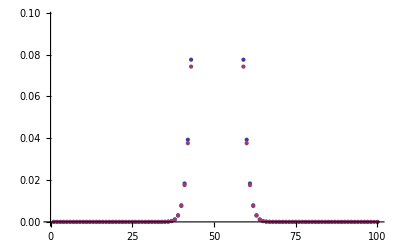

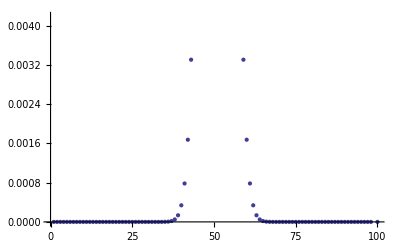

```mathematica
(*ListPlot3D[config-configi,PlotRange->{-0.1,0.1}]*)
ListPlot[{config[[50,;;]],configi[[50,;;]]}]
ListPlot[config[[50,;;]]-configi[[50,;;]]]
```

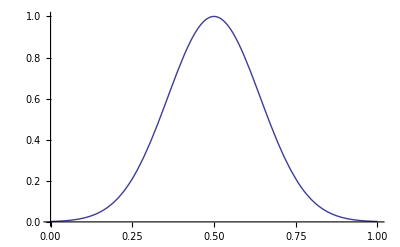

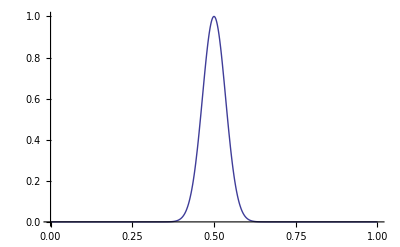

```mathematica
Plot[Exp[-(x-0.5)^2/(0.2)^2],{x,0,1},PlotRange->{0,1}]
Plot[Exp[-(x-0.5)^2/(0.05)^2],{x,0,1},PlotRange->{0,1}]
```